```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/student/compphys/week8

```mathematica
data=Partition[ReadList["!./mdgas .001 100000 30 10 2.0",Number],121];
```

```mathematica
display[l_,n_,sz_]:=Graphics[{{FaceForm[],EdgeForm[Black],Rectangle[{0,0},{sz,sz}]},AbsolutePointSize[6],Table[Point[{l[[2+4*i]],l[[3+4*i]]}],{i,0,n-1}]},PlotRange->{{-0.2,sz+0.2},{-0.2,sz+0.2}}]
```

```mathematica
ListAnimate[Table[display[data[[i]],30,10],{i,1,20000,100}]]
```

```mathematica
lj[r1_,r2_]:=Module[{r=Norm[r1-r2]},4(1/r^12-1/r^6)]
pot[l_,n_]:=Sum[lj[{l[[2+4*i]],l[[3+4*i]]},{l[[2+4*j]],l[[3+4*j]]}],{i,0,n-1},{j,i+1,n-1}]
```

```mathematica
pot[data[[1]],30]
```

-60.8597

```mathematica
ken[l_,n_]:=0.5Sum[l[[4+4*i]]^2+l[[5+4*i]]^2,{i,0,n-1}]
```

```mathematica
ken[data[[1]],30]
```

90.8597

```mathematica
e=Table[pot[d,30]+ken[d,30],{d,data[[;;;;100]]}];
```

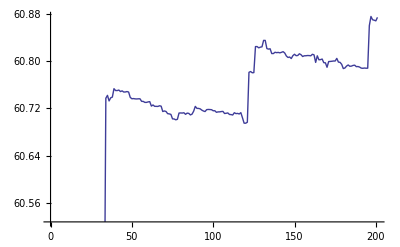

```mathematica
ListLinePlot[e]
```

```mathematica
(* compute K every 100 integration steps *)
kineticen=Table[ken[d,30],{d,data[[;;;;100]]}];
```

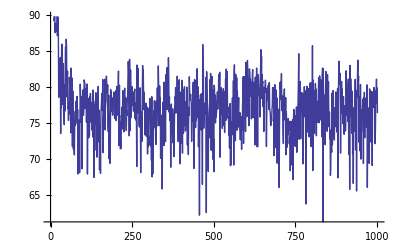

```mathematica
(* Note tha until we get to step 50*100 the system is
still not "thermalized" -- the kinetic energy drifts *)
ListLinePlot[kineticen]
```

```mathematica
(*If we take that data after the first 100*100 steps and average it we get the average of K in the "thermalized" state *)
Mean[kineticen[[100;;]]]
```

76.6792

```mathematica
(*The temperature is then kT = <K>/N *)
Print["kT: ",%/30]
```

kT: 2.55597